Gaussovo pravidlo - výpočet uzlů
Autor: David Poledne
Datum: 6. května 2025

Popis:
Tento skript počítá uzly  gaussova pravidla řádu d.

```mathematica
Remove["Global`*"]

(*Algebraický řád kvadratury*)
d=3;

(*Rozdělení uzlů podle typů*)
(*Import rozložení*)
SetDirectory[NotebookDirectory[]];
nds=Rest[Import["rozložení uzlů.csv"]];
(*Zobrazení tabulky rozložení uzlů*)
TableForm[nds,TableHeadings->{None,{Subscript[n,0],Subscript[n,1],Subscript[n,2]}}]

(*Zadání polárních momentů*)
v[0,0]=1;
v[2,0]=1/4;
v[3,3]=-1/10;
v[4,0]=1/10;
v[5,3]=-2/35;
v[6,0]=29/560;
v[6,6]=1/28;
v[7,3]=-1/28;
v[8,0]=11/350;
v[8,6]=1/40;

vrchol1={-1,0};
vrchol2={1/2,Sqrt[3]/2};
vrchol3={1/2,-Sqrt[3]/2};
v[{0,0}]=1;
verticesPoints={vrchol1,vrchol2,vrchol3};
triangle=Triangle[verticesPoints];

(*Počet neznámých v soustavě rovnic(s n0)*)
n=nds[[d,2]]+nds[[d,3]]+1;

(*Vytvoření listu proměnných pro w, r, θ*)
wList=Table[Subscript[w,i],{i,n}];
rList=Table[Subscript[r,i],{i,n}];
θList=Table[Subscript[θ,i],{i,n}];

(*Určení rovnic*)
eq1=wList[[1]]+Sum[wList[[i]],{i,2,nds[[d]][[2]]+1}]+Sum[wList[[i]],{i,nds[[d]][[2]]+2,nds[[d]][[2]]+nds[[d]][[3]]+1}]==1;
eq2=Table[
If[EvenQ[j+3k], Sum[wList[[i]] rList[[i]]^j,{i,2,nds[[d]][[2]]+1}]+Sum[wList[[i]] rList[[i]]^j Cos[3 k θList[[i]]],{i,nds[[d]][[2]]+2,nds[[d]][[2]]+nds[[d]][[3]]+1}]==v[j,3 k],Nothing
],{j,2,d},{k,0,Floor[j/3]}];
equations={eq1,eq2}//Flatten;
If[nds[[d]][[1]]==0,{Subscript[w,1]=0,wList=Delete[wList,1]},Nothing];
If[nds[[d]][[3]]==0,θList={},Nothing];
If[nds[[d]][[3]]!=0,θList=Drop[θList,n-nds[[d]][[3]]],Nothing];
rList=Delete[rList,1];
equations={eq1,eq2}//Flatten

(*Řešení soustavy*)
(*Určení proměnných*)
variables={wList,rList,θList}//Flatten;
solution = N[Solve[equations,variables]]

(*Volba řešení*)
solution = solution[[1]]/. C[1]->0
```

n_0 | n_1 | n_2
1 | 0 | 0
0 | 1 | 0
1 | 1 | 0
0 | 2 | 0
1 | 2 | 0
0 | 2 | 1
1 | 2 | 1
1 | 3 | 1
1 | 4 | 1
0 | 4 | 2

{w_1+w_2==1,r_2^2 w_2==1/4,r_2^3 w_2==-1/10}

{{w_1→-0.5625,w_2→1.5625,r_2→-0.4}}

{w_1→-0.5625,w_2→1.5625,r_2→-0.4}

{{-0.5625,{0,0}},{0.520833,{-0.4,0}},{0.520833,{0.2,-0.34641}},{0.520833,{0.2,0.34641}}}

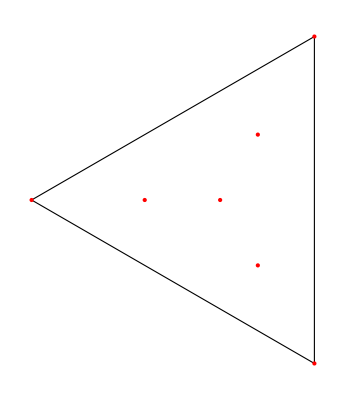

```mathematica
(*množina všech uzlů*)
nodes={};
(*uzly nultého a prvního typu s váhami*)
If[nds[[d]][[1]]==1,AppendTo[nodes,{Subscript[w,1]/.solution,{0,0}}],Nothing];

nodesNew=Table[{Subscript[w,j]/3,{Subscript[r,j]Cos[2Pi i/3],Subscript[r,j]Sin[2Pi i/3]}},{j,2,nds[[d]][[2]]+1},{i,0,2}]/.solution;

(*Uzly druhého typu*)
nodesSecTyp1=Table[{Subscript[w,j]/6,{Subscript[r,j]Cos[Subscript[θ,j]+2Pi i/3],Subscript[r,j]Sin[Subscript[θ,j]+2Pi i/3]}},{j,nds[[d]][[2]]+2,nds[[d]][[2]]+nds[[d]][[3]]+1},{i,0,2}]/.solution/.C[1]->0;
nodesSecTyp2=Table[{Subscript[w,j]/6,{Subscript[r,j]Cos[-Subscript[θ,j]+2Pi i/3],Subscript[r,j]Sin[-Subscript[θ,j]+2Pi i/3]}},{j,nds[[d]][[2]]+2,nds[[d]][[2]]+nds[[d]][[3]]+1},{i,0,2}]/.solution/.C[1]->0;

nodesNew=Flatten[nodesNew,1];  
If[nds[[d]][[3]]==0,nodes=Join[nodes,nodesNew],nodes=Join[nodes,nodesNew,nodesSecTyp1[[1]],nodesSecTyp2[[1]]]]


(*Grafické vykreslení uzlů*)
nodesOnly=Table[nodes[[i]][[2]],{i,1,Length[nodes]}];
verticesPoints={{-1,0},{1/2,Sqrt[3]/2},{1/2,-Sqrt[3]/2}};
allPoints=Join[nodesOnly,verticesPoints];
Graphics[{EdgeForm[Black],FaceForm[],Polygon[{{-1,0},{1/2,Sqrt[3]/2},{1/2,-Sqrt[3]/2}}],Red,PointSize[Large],Point[allPoints] }]
```

```mathematica
(*uzly nultého a prvního typu, přirozené souřadnice, s váhami*)
nodesNatCoo={};
If[nds[[d]][[1]]==1,{AppendTo[nodesNatCoo,{Subscript[w,1]/.solution,{1/3,1/3,1/3}}]},Nothing];
nodesNewNatCoo=Table[{Subscript[w,j]/3/.solution,{(1-2Subscript[r,j])/3,(1+Subscript[r,j])/3,(1+Subscript[r,j])/3}},{j,2,nds[[d]][[2]]+1}]/.solution;
nodesNatCoo=Join[nodesNatCoo,nodesNewNatCoo];

(*uzly nultého a prvního typu, přirozené souřadnice, všechna, s váhami*)
nodesNatCooAll={};
If[nds[[d]][[1]]==0,nodesPrvniTyp=Table[{{Subscript[w,j+1]/3/.solution,{nodesNatCoo[[j]][[2]][[1]],nodesNatCoo[[j]][[2]][[2]],nodesNatCoo[[j]][[2]][[3]]}},{Subscript[w,j+1]/3/.solution,{nodesNatCoo[[j]][[2]][[2]],nodesNatCoo[[j]][[2]][[1]],nodesNatCoo[[j]][[2]][[3]]}},{Subscript[w,j+1]/3/.solution,{nodesNatCoo[[j]][[2]][[2]],nodesNatCoo[[j]][[2]][[3]],nodesNatCoo[[j]][[2]][[1]]}}},{j,1,nds[[d]][[2]]}],
{nodesPrvniTyp=Table[{{Subscript[w,j]/3/.solution,{nodesNatCoo[[j]][[2]][[1]],nodesNatCoo[[j]][[2]][[2]],nodesNatCoo[[j]][[2]][[3]]}},{Subscript[w,j]/3/.solution,{nodesNatCoo[[j]][[2]][[2]],nodesNatCoo[[j]][[2]][[1]],nodesNatCoo[[j]][[2]][[3]]}},{Subscript[w,j]/3/.solution,{nodesNatCoo[[j]][[2]][[2]],nodesNatCoo[[j]][[2]][[3]],nodesNatCoo[[j]][[2]][[1]]}}},{j,2,nds[[d]][[2]]+1}],AppendTo[nodesNatCooAll,{Subscript[w,1]/.solution,{1/3,1/3,1/3}}]}];
nodesPrvniTyp=Flatten[nodesPrvniTyp,1];
nodesNatCooAll=Join[nodesNatCooAll,nodesPrvniTyp];

(*uzly druhého typu, přirozené souřadnice, s váhami, všechna*)
vrchol1Ref={-1,0};
vrchol2Ref={1/2,Sqrt[3]/2};
vrchol3Ref={1/2,-Sqrt[3]/2};

verticesPoints={vrchol1Ref,vrchol2Ref,vrchol3Ref};
triangleRef=Triangle[verticesPoints];
areaRef=RegionMeasure[triangleRef];

If[nds[[d]][[1]]==1,nodesSecTypNatCoo=Table[{nodes[[i]][[1]],{RegionMeasure[Triangle[{nodes[[i]][[2]],vrchol2Ref,vrchol3Ref}]]/areaRef,RegionMeasure[Triangle[{vrchol1Ref,nodes[k[i]][[2]],vrchol3Ref}]]/areaRef,RegionMeasure[Triangle[{vrchol1Ref,vrchol2Ref,nodes[[i]][[2]]}]]/areaRef}},{i,nds[[d]][[2]]*3+2,nds[[d]][[2]]*3+nds[[d]][[3]]*6+1}],nodesSecTypNatCoo=Table[{nodes[[i]][[1]],{RegionMeasure[Triangle[{nodes[[i]][[2]],vrchol2Ref,vrchol3Ref}]]/areaRef,RegionMeasure[Triangle[{vrchol1Ref,nodes[[i]][[2]],vrchol3Ref}]]/areaRef,RegionMeasure[Triangle[{vrchol1Ref,vrchol2Ref,nodes[[i]][[2]]}]]/areaRef}},{i,nds[[d]][[2]]*3+1,nds[[d]][[2]]*3+nds[[d]][[3]]*6}]
];
nodesSecTypNatCoo;
nodesNatCooAll=Join[nodesNatCooAll,nodesSecTypNatCoo]
```

{{-0.5625,{1/3,1/3,1/3}},{0.520833,{0.6,0.2,0.2}},{0.520833,{0.2,0.6,0.2}},{0.520833,{0.2,0.2,0.6}}}